# L Nl Pet Site

```mathematica
(*Shared random onsite potential generator*)
generateG[t_,W_,K_]:=RandomReal[{-2W-0t,2W+0t},K];

(*ml matrix:tridiagonal with random onsite+constant hopping*)
makeML[t_,W_,K_]:=Module[{g,Ox},g=generateG[t,W,K];
Ox=ConstantArray[0,{K,K}];
Do[Ox[[i,i]]=g[[i]],{i,1,K}];
Do[Ox[[i+1,i]]=t;Ox[[i,i+1]]=t,{i,1,K-1}];
Rationalize[Ox,Power[10,-20]]];

(*mnl matrix:exponential decay hopping+random onsite*)
makeMNL[t_,W_,K_,l_,c_]:=Module[{g,Ox},g=generateG[t,W,K];
Ox=Table[l/c^Abs[i-j],{i,1,K},{j,1,K}];
Do[Ox[[i,i]]=g[[i]],{i,1,K}];
Rationalize[Ox,Power[10,-20]]];

(*mpet matrix:modified Petersen graph adjacency+random onsite+exponential decay*)
makeMPET[t_,W_,K_,l_,c_]:=Module[{g,mat,p},g=generateG[t,W,K];
p=PetersenGraph[K/2,K/4];
mat=WeightedAdjacencyMatrix[p];
Do[mat[[i,i]]=g[[i]],{i,1,K}];
Do[Do[If[i=!=j,mat[[i,j]]=l*mat[[i,j]]/c^Abs[i-j]],{j,1,K}],{i,1,K}];
Normal[Rationalize[mat,Power[10,-20]]]];
(*Module to compute neutrino masses and mixing matrices*)NeutrinoLocalMass[t_,W_,K_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,hamr,yukr},vr=Rationalize[v,Power[10,-pr]];
hamr =Rationalize[ham,Power[10,-pr]]; 
yukr =Rationalize[yuk,Power[10,-pr]]; 
ml1=makeML[t,W,K];ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];ml5=makeML[t,W,K];ml6=makeML[t,W,K];
 TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoNonLocalMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]]; ml1=makeMNL[t,W,K,l,c];ml2=makeMNL[t,W,K,l,c];ml3=makeMNL[t,W,K,l,c];ml4=makeMNL[t,W,K,l,c];ml5=makeMNL[t,W,K,l,c];ml6=makeMNL[t,W,K,l,c];TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoPetMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];ml1=makeMPET[t,W,K,l,c];ml2=makeMPET[t,W,K,l,c];ml3=makeMPET[t,W,K,l,c];ml4=makeMPET[t,W,K,l,c];ml5=makeMPET[t,W,K,l,c];ml6=makeMPET[t,W,K,l,c];TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoLocalMajoranaMass[t_,W_,K_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];Wr=Rationalize[W,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]]; ml1=makeML[t,W,K];ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];ml5=makeML[t,W,K];ml6=makeML[t,W,K];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoNonLocalMajoranaMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];Wr=Rationalize[W,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];ml1=makeMNL[t,W,K,l,c];ml2=makeMNL[t,W,K,l,c];ml3=makeMNL[t,W,K,l,c];ml4=makeMNL[t,W,K,l,c];ml5=makeMNL[t,W,K,l,c];ml6=makeMNL[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoPetMajoranaMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];Wr=Rationalize[W,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];ml1=makeMPET[t,W,K,l,c];ml2=makeMPET[t,W,K,l,c];ml3=makeMPET[t,W,K,l,c];ml4=makeMPET[t,W,K,l,c];ml5=makeMPET[t,W,K,l,c];ml6=makeMPET[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
```

```mathematica
(*Set global parameters*)t=0.2;
c=2.0;
W=5;
K=12;
l=t*c;
v=0.173;
```

```mathematica
yukawa = IdentityMatrix[3]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
yukawa={{1,0.4,0.7},{0.4,1,0.5},{0.7,0.5,1}};
```

```mathematica
nlm=makeML[t,W,K]//N;
nlm2=makeMNL[t,W,K,l,c]//N;
nlm3=makeMPET[t,W,K,l,c]//N;
ev1=Abs[Eigenvalues[nlm]];ev2=Abs[Eigenvalues[nlm2]];ev3=Abs[Eigenvalues[nlm3]];
ec1=Inverse[Eigenvectors[nlm]];ec2=Inverse[Eigenvectors[nlm2]];ec3=Inverse[Eigenvectors[nlm3]];
```

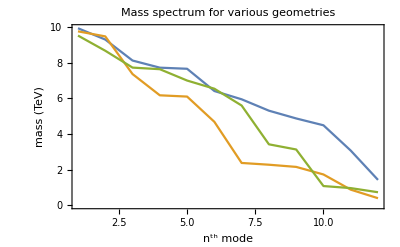

```mathematica
ListLinePlot[{ev1,ev2,ev3},PlotRange->{{1,K},All},PlotLegends->Placed[Framed[PointLegend[{RGBColor[0.368417,0.506779,0.709798],RGBColor[0.880722,0.611041,0.142051],RGBColor[0.560181,0.691569,0.194885]},{"Local","Non-Local","Petersen"},LegendMarkers->{Style["-",FontSize->14],Style["-",FontSize->14],Style["-",FontSize->12]   },LegendMarkerSize->12,LabelStyle->{FontSize->13}],Background->Directive[White,Opacity[0.3]],FrameStyle->Gray,RoundingRadius->5,FrameMargins->0],Scaled[{0.820,0.770}]],Frame->True,FrameTicksStyle->Directive[Black,FontSize->15],FrameLabel->{Style["n^th mode",Black,FontSize->15],Style["mass (TeV)",Black,FontSize->15]},LabelStyle->Black,PlotLabel->Style["Mass spectrum for various geometries",FontSize->15]]
```

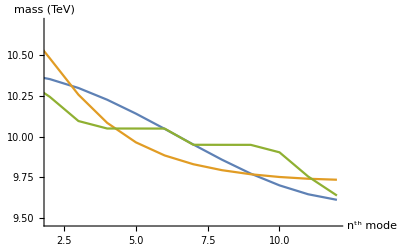

```mathematica
ListLinePlot[{ev1,ev2,ev3},PlotRange->{{2,K},All},PlotLegends->Placed[Framed[PointLegend[{RGBColor[0.368417,0.506779,0.709798],RGBColor[0.880722,0.611041,0.142051],RGBColor[0.560181,0.691569,0.194885]},{"Local","Non-Local","Petersen"},LegendMarkers->{Style["-",FontSize->12],Style["-",FontSize->12],Style["-",FontSize->12]   },LegendMarkerSize->5,LabelStyle->{FontSize->8}],Background->Directive[White,Opacity[0.3]],FrameStyle->Gray,RoundingRadius->5,FrameMargins->0],Scaled[{0.80,0.80}]],AxesLabel->{Style["n^th mode",Black],Style["mass (TeV)",Black]},PlotRangePadding->Scaled[0.1],PlotLabel->""]
```

```mathematica
Min[ev1]
Max[ev1]
```

0.00179432

0.424485

```mathematica
Sum[ec1[[1,i]]*ec1[[K,i]]/(ev1[[i]]-0),{i,1,K}]
f[n_]:=Sum[ec1[[1,i]]*ec1[[K,i]]/(n+ev1[[i]]),{i,1,K}]
g[n_]:=Sum[ec2[[1,i]]*ec2[[K,i]]/(n+ev2[[i]]),{i,1,K}]
h[n_]:=Sum[ec3[[1,i]]*ec3[[K,i]]/(n+ev3[[i]]),{i,1,K}]
```

-1.19208

```mathematica
Plot[{Log10[Abs[f[x]]],Log10[Abs[g[x]]],Log10[Abs[h[x]]],Log10[1/x]},{x,0,100},PlotRange->{{0.1,100},All},PlotLegends->Placed[SwatchLegend[{Style["Local",Black,14],Style["Non-Local",Black,14],Style["Petersen",Black,14],Style["1/n",Black,14]},LegendFunction->(Framed[#,RoundingRadius->8,FrameStyle->Black,Background->White]&)],{1,0.5}],FrameTicksStyle->Directive[Black,FontSize->16],Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]]
,FrameLabel->{Style["n",Black,18],Style["Log10 of ζ",Black,18]},LabelStyle->Directive[Black,14],PlotLabel->""]
```

-Graphics-

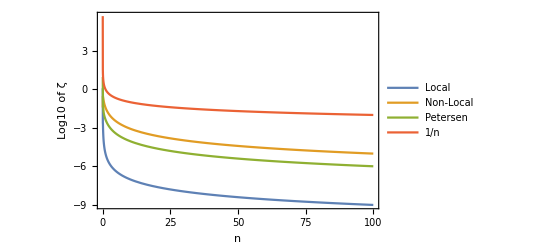

```mathematica
Plot[{Log10[Abs[f[x]]],Log10[Abs[g[x]]],Log10[Abs[h[x]]],Log10[1/x]},{x,0,100},PlotRange->{{0.01,100},All},PlotLegends->{"Local","Non-Local","Petersen","1/n" },Frame->True,FrameLabel->{Style["n",Black],Style["Log10 of ζ",Black]},LabelStyle->Black,PlotLabel->""]
```

```mathematica
f[0.124]
```

-0.101325

```mathematica
(*Create a list of 2 entries with random numbers between 0 and 1*)list=RandomReal[{1,2},2];
```

```mathematica
newList=Table[50+list[[i]],{i,Length[list]}]
```

{51.1141,51.9617}

```mathematica
1/list[[1]]-1/list[[2]]
```

0.387822

```mathematica
1/newList[[1]]-1/newList[[2]]
```

0.000319141

```mathematica
nlm2=NeutrinoNonLocalMass[t,W,K,l,c,0,0,0,yukawa,v,30]
```

{{0.741058274938426444991180590956,0.698329338576945106022239065532,0.690051591769806156926160381342,0.519587589616362135322815478734,0.502649419239066055052867406793,0.473294506376758706855304092516,0.380431867574620483782518705623,0.310792287078850313174227066627,0.301227897928895397160133023562,0.297354781244714861406740396842,0.288502145894079985818131643391,0.272561773280228519428605644415,0.266776609329071692490117455084,0.263022417533122408714141036338,0.257545911002479862119426563088,0.255044205870564072421299263235,0.250535306749507092411100232835,0.245327320209716776244235813382,0.235976838571283406625349686835,0.232255499962502373154491420805,0.22441678977116142741954107138,0.212829562908762398918037960384,0.206643723666701728180277202037,0.195321163690433016949312310998,0.189466189538545673068411621223,0.179878178580395939644244005613,0.169919019598581335724231412879,0.14893734332494151947804999027,0.14388665428155350414584756796,0.131611322669864443547833209291,0.123467768622531793837441782378,0.108547105731454091434712507317,0.0954706557156820041420157330053,0.0622776846486293052370567440287,0.0530428300419692706342956944851,0.0415852212693469261422469927623,0.0396772123209192111375151960033,0.0289210068557902455297348502001,0.0157189047398396868203342446686},(0.377669540926115013055185731788 | -0.230324909590626569299162714758 | 0.230221512909052665809003162378
0.0673244577584504043324543271357 | 0.526337407127414414264534003372 | 0.216653900257956157220253427768
0.0647780574429497363097644906804 | 0.0489719481426081264003578369637 | -0.533414781901791034656355335424)}

```mathematica
nlm3=NeutrinoPetMass[t,W,K,l,c,0,0,0,yukawa,v,30]
```

{{0.440428371118278560085282634937,0.389708176576172049837056467349,0.386743703913416481170799022487,0.382207387673701287807603840786,0.362876333866307939186929623392,0.359855574622048313175563623052,0.321842857795729767858495585014,0.268502983031941706310273979114,0.252550621380090572837181499095,0.246103408050609232462872350447,0.236892197995975734484952183974,0.231285631284197071859266893328,0.197439617863688829437682551373,0.190413419540759337655501166315,0.183684358341949619080973253001,0.18141796414523470962035625104,0.147900856360981524178399866352,0.133574922250760222122933777285,0.118039564686631999829857941726,0.107751516337215043484511398159,0.106947258259090322389865689261,0.104460283863524402673263028391,0.103615489646583899199030498023,0.0977435849449963552526472962566,0.0897663531286179968366761452824,0.0856794307806296496522978606638,0.0783060881218411575512975374559,0.0749119646797647351180536043423,0.0709529138315825719698734280047,0.0508549362088366524809309666705,0.04949038699908640399696358024,0.0362292831059508858925169482454,0.0335278764913918737961905282607,0.0263646435992172834336103339779,0.00528812912480067827963473644515,0.00325476956768186578201203723161,0.00187492339066199922364424703131,0.000882875185006527889452747182706,0.000777414284746570374168314266433},(0.0926643356625961311615066014481 | -0.118898955787187033970852479304 | 0.247559939510723308009793507762
-0.131718914007501868501081632655 | -0.123380555875609776471514425891 | 0.000691733399471912572291956713406
-0.117216979717326033511440018664 | 0.110252900987669995679513581212 | 0.0929218130857998675079971890036)}

```mathematica
pr=30;vr=Rationalize[v,Power[10,-pr]];xr=Rationalize[0.2,Power[10,-pr]];yr=Rationalize[0.3,Power[10,-pr]];zr=Rationalize[0.4,Power[10,-pr]];Wr=Rationalize[W,Power[10,-pr]];yukr =Rationalize[yukawa,Power[10,-pr]];
```

```mathematica
ml1=makeML[t,W,K];ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];ml5=makeML[t,W,K];ml6=makeML[t,W,K];
 TotalML=ArrayFlatten[{{ml1,xr*ml2,yr*ml3},{xr*ml2,ml4,zr*ml5},{yr*ml3,zr*ml5,ml6}}];
```

```mathematica
ec2=Eigenvectors[N[ml1]]
ev2=Eigenvalues[N[ml1]]
```

(0.11119 | 0.206123 | 0.429671 | 0.553981 | 0.533853 | 0.345378 | 0.186696 | 0.100461 | 0.0549225 | 0.0308417 | 0.0180044 | 0.0106444
0.0149274 | -0.0353609 | 0.041603 | -0.0667166 | 0.124079 | -0.248195 | 0.406161 | -0.496947 | 0.497065 | -0.413653 | 0.271541 | -0.107278
-0.117652 | -0.164618 | -0.239467 | -0.150146 | 0.046578 | 0.20744 | 0.291894 | 0.356923 | 0.404283 | 0.425808 | 0.408991 | 0.330671
0.279453 | -0.563179 | 0.42176 | -0.322535 | 0.265176 | -0.25672 | 0.192509 | -0.0283912 | -0.150945 | 0.251546 | -0.227512 | 0.104477
0.228441 | -0.429416 | 0.248028 | -0.0578398 | -0.132679 | 0.329686 | -0.41041 | 0.222522 | 0.114799 | -0.37668 | 0.400877 | -0.196306
0.273908 | 0.332386 | 0.385439 | 0.102674 | -0.272603 | -0.387369 | -0.287519 | -0.115144 | 0.084314 | 0.262726 | 0.368694 | 0.350753
0.369007 | 0.322083 | 0.160185 | -0.195844 | -0.308698 | -0.0213882 | 0.285057 | 0.422492 | 0.316632 | 0.0238775 | -0.283595 | -0.399151
-0.191435 | 0.265387 | 0.0279272 | -0.306469 | 0.432027 | -0.36552 | -0.0102795 | 0.374279 | -0.302241 | -0.117555 | 0.405165 | -0.261626
0.519351 | 0.26224 | -0.184962 | -0.339958 | 0.0522345 | 0.357499 | 0.211388 | -0.137824 | -0.356964 | -0.234076 | 0.119213 | 0.347968
0.256695 | -0.239834 | -0.217331 | 0.46131 | -0.266505 | -0.167235 | 0.383878 | 0.0136621 | -0.389111 | 0.140976 | 0.3294 | -0.300367
0.413676 | 0.0400011 | -0.379 | -0.0445271 | 0.379793 | 0.0170163 | -0.374192 | -0.253115 | 0.210172 | 0.386281 | 0.0244782 | -0.372888
0.297839 | -0.12271 | -0.341792 | 0.292498 | 0.187786 | -0.401627 | -0.115682 | 0.387484 | 0.16966 | -0.366294 | -0.205836 | 0.358384)

{0.43551,-0.409019,0.344591,-0.338305,-0.3112,0.307451,0.23932,-0.212508,0.16574,-0.122111,0.0840918,-0.0176481}

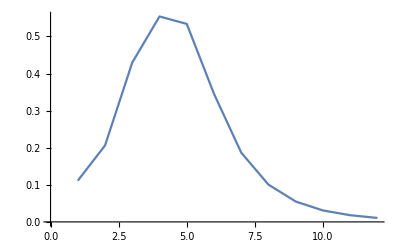

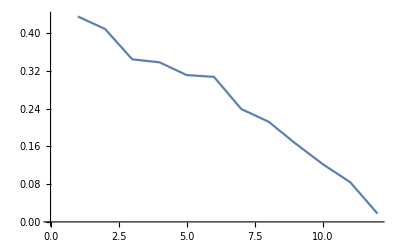

```mathematica
ListLinePlot[Abs[{ec2[[1]]}]]
ListLinePlot[Abs[{ev2}]]
```

```mathematica
Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
```

```mathematica
SymmetricMatrixQ[Mn]
```

True

```mathematica
ec=Eigenvectors[Mn];
```

```mathematica
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
```

```mathematica
ec=Eigenvectors[SetPrecision[Mn,pr]];
```

```mathematica
Iec=Inverse[ec];
```

```mathematica
L1=Iec[[K]];L2=Iec[[2 K]];L3=Iec[[3 K]];R1=Iec[[1+3*K]];R2=Iec[[1+K+3*K]];R3=Iec[[1+2 K+3*K]];
```

```mathematica
evalue//Diagonal
```

{16.7005021595169868473543899449,16.700451234810887288388795094,16.6516236405360532155929260441,16.6515341668538021977210728069,16.5497765996146308922851256486,16.5496040601865967235047801468,16.4490031597467507822190983351,16.4487420883205837096831294291,16.3030121567666904956754248624,16.3026816941623566763074604833,16.1532412981166315760461169377,16.1529203729821480819559125188,16.0017481520813308801861340788,16.0012919612794529653881179844,15.8465699711646149385097118732,15.8462307059549430762955055648,15.7167973222932310155602536298,15.7165534254886540462132311878,15.5917308304217948462973782201,15.5915416167143598626111481608,15.5084403698960341084857235018,15.5083884602753217425386781446,15.4455095745168735854921563913,15.445500030994211798740967924,10.012067359950928414387376051,10.0060726311431239123743179042,9.99748458393614372693418754444,8.4612019983009486689351228235,8.46093716017577644059853267694,8.43510145510770585894632496968,8.43494381084801037997741762835,8.37291417698059891740729449831,8.37171663036089721953277403589,8.31250601052323645531404485458,8.3105498436216389992956041452,8.25484036579563315620873582416,8.25206276474692631784425796418,8.18144485731657799297649409475,8.18027699470160541846752376338,8.11400503508907660532163258242,8.11207079053822092342770243603,8.01732484882655949194847523097,8.01662754535733343897477989219,7.94539147949730446137281012081,7.94462885131707273915763612327,7.87671431135102632188388791626,7.87591852663005158881487191567,7.8541648186848322280468348628,7.85382968764468374949534281062,7.81349590679421464237235440209,7.81347529796413094864077921883,6.05154393046279277970541469918,6.05153028064663748604049029312,6.01356652480296419683068386864,6.01325362108840094548797022728,5.97347448801819613209090523966,5.97290015708332197470860765581,5.94838902149782962736750177505,5.94733169486402472269937412045,5.89083524748404641982544969111,5.88962962658931635092770118479,5.83877038176909838606784904909,5.83777157302551511140645061199,5.78231837828900906389976642261,5.78185471445519959135204352644,5.72151595449068215070119826945,5.7208492214784515849043274999,5.67509619809669459437998811412,5.67490213457898309725600240441,5.63572900461307570511766425544,5.63540581546672684962418088618,5.59380785248639669645079079519,5.59355087248756709874338846359,5.57768144540216353889912318021,5.57767608433167004664106653338}

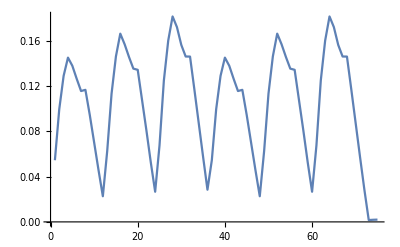

```mathematica
ListLinePlot[Abs[{ec[[1]]}]]
```

```mathematica
L1
```

{-1.76917216639192332375535714528×10^-15,-0.0286555825546109641446527208333,0.0286834347578162669607041642566,-0.0628370314695792945386917723244,-0.0629101481369422745678519680955,-0.0639049647162246603121045990939,0.0640290394119081150244270101809,-0.106445833335954935337572686798,-0.106630482446206247840029191807,-0.150875574828385260340750547422,0.150989337017745681545793126272,-0.149364711571590895899219030519,-0.149349106626427423597336110002,-0.133962318561723592793343030108,0.133873502609192312745390930426,-0.11144660543836513919239581144,-0.111355672594117843871015417807,-0.106250281366387300929655953541,0.106193768927647564425573312951,0.124575264247911416623931993012,0.124483433504594887621675158358,-0.0703849453909856263115514792885,-0.0703295482701358224234326416427,-0.0390215827864750307426569402744,0.0389065014899855818360005104712,-0.0624291056751266054287871394923,0.0625559216534631392885796202307,-0.13000397591052669707769868141,-0.131102415547393017153321391011,-0.113244797523358610532731335508,0.114719271442591326187183487478,0.140890775722891333269248715854,0.139104399373068018454088852387,-0.207521927607587867780743790862,0.208136906742770831570040668646,0.167823830775235510501419475015,0.16835017148668862102321919361,0.258483289429548822987822272952,0.258732441811420822997016536005,-0.201175541309713994838967536985,0.200814257696139855346146068246,0.264291186362699988041654302625,-0.263431992178369534490898590878,-0.158833308478338164306971013675,0.158591813290362721419288060132,-0.0974056572176115911812193468658,0.0973000135675399966470308417178,0.012821070412363996943713355134,0.0126576375279748132630706342419,-1.93433999763594303756925888723×10^-9,0.0236333826260361090131952596417,0.0236377003901406307936072080596,0.0133853890025652569620480162057,0.0140253150095040959271630310634,-0.0243272465504775673266226437957,-0.0257891415066293631110454510363,0.0740605613758142159183099980611,0.0747965542984027951415244554985,-0.106335368077184136623481252716,0.105666341516547010987601951736,0.0827651912055550814605754090369,0.0829687797288940061805212732638,0.0532777554550763773565250936723,0.0531202072315904940440063562007,-0.0286238607628013098039526083292,-0.0273592759347296273035271884621,0.0282398326412153194438519400638,-0.0281808921544894641439024541031,0.0544751690913492769621865816208,-0.0545388958767219051033862987552,-0.0443548182188876724701574925838,0.0442604570797005559965210493319,0.00330804212075379394963897968458,-0.00328134107980957540997040851384,-3.12278652015623337409225511693×10^-18}

```mathematica
L2
```

{-2.02778018413751647882617534994×10^-15,-0.0327768838187440965916607442853,0.0328087414337962526976627660934,-0.0718726274901525096756283693885,-0.071956255064211905282806989987,-0.0730916891953625242281072522901,0.0732335879066720427850037584552,-0.121742908472560234044866197647,-0.121954072790172392024272954092,-0.172550503185895945830982380906,0.172680583100760375608673896702,-0.170816265314729492685941456643,-0.170798392537853750996436006637,-0.153197087190227537697209772275,0.153095499849615384143570785287,-0.127445863856516664587643412827,-0.127341867652632880225981370931,-0.12150255888848976785781421462,0.121437932961532097034307843923,0.142458370327737360577773878485,0.14235335839317224140203412828,-0.0804894915755692917401876014051,-0.0804261431588649581168591765077,-0.0446238217374461272743541672399,0.0444922189106027063459919961085,0.0416952839787740456645111105274,-0.0417799957479142030367063652517,0.0868629103450377186855517688285,0.0875970898195039255070972513224,0.0756974850197552699291678658644,-0.0766845456750916199729065125352,-0.0942272075028700900610524413365,-0.093033702261111967018880415505,0.138961169614536574589281798584,-0.139373872678987805211284620059,-0.112501579933021407383211809469,-0.112856716751414981167277748581,-0.173491069177427808990892909989,-0.173660419591521849870741588161,0.135195716883798773090043621827,-0.134955639303317779226319367097,-0.177822251574848978615234490953,0.177245117456213887775012925534,0.107025419623424880977618979885,-0.106863021345858773409349649098,0.0657176727567286277964137171035,-0.0656464901380563691709358853974,-0.00865757895541219459495224667289,-0.00854726205333705632182117862683,-4.13147277434752129177810923999×10^-9,0.0530402779167044973168465868965,0.0530499832673921241083981819002,0.0301711227083685509795648293042,0.0316165112730336557047028497986,-0.0550093453530471541349337835562,-0.058330822368343755134097941606,0.168080870045109678602496478361,0.169767316043727859052437981621,-0.242126079107119751219778110027,0.240613030987301241490616240825,0.18940007697070772836443336292,0.189874538483166978483247997931,0.122354309839568129080966661548,0.122004843415296839449910471944,-0.0659160916391805015032511661703,-0.0630114130826724140396355684219,0.0652946828846929070169540587713,-0.0651591769306249932454049932713,0.126343983316873872449580745391,-0.126492066682112782017788886499,-0.102961765537930334173092021887,0.102742883280396005041884249249,0.00768917892923846050124563502009,-0.00762714486646626232114679553687,-6.61836259245667413254673812847×10^-18}

```mathematica
N[Transpose[Lmat],2] ==Transpose[Rmat]
```

False

```mathematica
ec[[-4]]
```

{0.015198767704403363237178841776,-0.0318244397360645487246777165899,0.0516975912050669650740353245247,-0.0175231938428366209332639143827,-0.0178047115621829242443187190188,0.0474497452890763996596489859422,-0.0636599269000211823392002064091,0.0725845419482576081593275792106,-0.0532117130833238652374864699804,0.062379872054702933922285959203,-0.0854996774640425998124370001234,0.0442604570797005559965210493319,0.0349877178732471036502162468849,-0.0744924260252342274804075701915,0.120579582337361250934753881683,-0.0394488795654622012995432227731,-0.0394737570538838471406845226219,0.111196798863615077792682647298,-0.150765052963440059959481835687,0.163694968950637219152961007613,-0.12426457463646972984421527905,0.143641316832855998783695430232,-0.220318403314322846280263011292,0.102742883280396005041884249249,-0.0445833643426038552083296496825,0.0942632604958219558316242784878,-0.152144539113328076254779011212,0.0505882282818515544835936068782,0.0507767025287777826336605331431,-0.138974563743715967000750682266,0.189634392985658441754168676078,-0.210199972974584216481370978165,0.154991799607772424530242999549,-0.181447075114760783828636668372,0.272259775867951151548015917339,-0.12912148190054357577703804813,0.0151033250882870711335049855403,-0.0318233086135559060813237281435,0.0516975777843617339323413108536,-0.0175231936851395107679541043906,-0.0178047115640114291952546852015,0.0474497452890975637422780358528,-0.0636599269000214231623443595403,0.0725845419482576108741043379736,-0.0532117130833238652675123857317,0.0623798720547029339226094094621,-0.0854996774640425998124403210746,0.0442604570797005559965210814552,0.0350842101533908752194876821881,-0.0744935528214451854895746476418,0.120579595719612200351201179699,-0.0394488797241658585473884448001,-0.0394737570519949910212063680348,0.111196798863592157819002881236,-0.150765052963439779975978677572,0.163694968950637215704982077968,-0.124264574636469729800865991067,0.143641316832855998783148880551,-0.220318403314322846280255955897,0.102742883280396005041884157018,-0.0445802820731811307746476131837,0.0942631670363752822337702137119,-0.152144537325659164682307142737,0.0505882282520286780784201217345,0.050776702529235987973975105916,-0.138974563743722651584150627164,0.18963439298565853799556751234,-0.210199972974584217867041562485,0.154991799607772424549946940532,-0.181447075114760783828915689478,0.27225977586795115154801989755,-0.129121481900543575777038105299,0.0064737846095678223163517920137,-0.0066530726282126860184573138826,-0.000710793405224410990751775340348}

```mathematica
Transpose[Lmat][[1]]
```

{0.0132015651470675558742448833578,0.000731448603229405339733389950527,0.0000505809148769922903084390144009,3.45898667845756504093498250942×10^-6,2.4030156250119610713202152402×10^-7,1.6635539395013958934634706077×10^-8,1.15475999156055320223392638559×10^-9,7.86894744498074058139761392221×10^-11,5.44624013014612075160614953942×10^-12,3.77292604689641882799845810084×10^-13,2.60605466788059766589642817444×10^-14,1.76917216639192332360007536597×10^-15,0.0131477768789624652497515662831,0.000838213070764544880137477429764,0.0000582759573399045695189673798869,4.01529209057239739200952418124×10^-6,2.79222937332976387257990880325×10^-7,1.92965720363432891783803937937×10^-8,1.33347106887271700457287462103×10^-9,9.16856221542083405455105601354×10^-11,6.24850040680188236862661409338×10^-12,4.41580105768024433091322216491×10^-13,2.98822587286433571338816218871×10^-14,2.02778018413751647864855391137×10^-15,0.0150294131654247030229571614904,0.000910397047382346331483539950223,0.0000633542300479104604456519874264,4.33633573379537439874181517631×10^-6,3.01407300240006364875453561398×10^-7,2.10541828904569019502953891815×10^-8,1.44893193877851259047071184696×10^-9,9.8789066956338225467915389102×10^-11,6.85214310995164155190979376487×10^-12,4.79243132777256539883188962349×10^-13,3.24163312423417079664632075753×10^-14,2.21567725277127674907476057164×10^-15,0.00985461219966721530481163360875,0.000758807472571891548452239696733,0.0000503528958126377760825589889751,3.46091467179097411886949837849×10^-6,2.40285111916029574101176022995×10^-7,1.66356810134593514940248574995×10^-8,1.15475876987538114319492706693×10^-9,7.86894850597215764878400694446×10^-11,5.4462400380768733576988901226×10^-12,3.77292605492190565465285258443×10^-13,2.60605466718426313344520194083×10^-14,1.76917216645260660183911182943×10^-15,0.0104907647515740312300891974861,0.000862937913807123876279346502374,0.0000580511146272075703721007296787,4.01729841978871306581784821118×10^-6,2.79205206930122742472516805673×10^-7,1.92967283359429221317824799251×10^-8,1.3334696976539619251931549737×10^-9,9.16856341390201933366483763309×10^-11,6.24850030153355930843289476986×10^-12,4.41580106683351707252734123598×10^-13,2.98822587206313351182967568908×10^-14,2.02778018420765265560523006817×10^-15,0.0116519834469556026101541214449,0.000939898745391380222947268406575,0.000063096066611663841239752452674,4.33859618014387455638147876067×10^-6,3.01387556464502559724808798531×10^-7,2.10543546550131429804392163327×10^-8,1.44893043828443639933938718368×10^-9,9.87890800905706671329131592806×10^-11,6.85214299568930662553650495038×10^-12,4.79243133771937018149676208285×10^-13,3.24163312336270443926223027705×10^-14,2.2156772528472641710091016559×10^-15,0.593611011637920225767658106132,0.50937497064754231629772509694,0.62228839698769454540712327241}

```mathematica
Transpose[Rmat][[2]]
```

{-0.0257203051588359706477343017677,-0.0511075303927207470076289689354,-0.0758028388011451905810468060943,-0.108829454322203531518901674594,-0.142241277075143370787913099015,-0.153204825408950088326957414337,-0.143737117830077851041966605694,-0.122755902453528780537160654493,-0.113482724644444037139621984135,-0.0979836822368275782365052380607,-0.0599673797057240184449668472638,-0.0286555825546109641446527208333,-0.0293705569723541035681778028417,-0.0599410493985093641232088578066,-0.0875881399846417780194682971323,-0.126699097977631219268392109024,-0.165552814565325169617088078747,-0.177832395840270605823157922812,-0.165781227291158664835655171751,-0.143568481500022382528581163067,-0.129588720720765571678665670475,-0.115536085250192150552538901595,-0.0682995172971370083673690419927,-0.0327768838187440965916607442853,-0.0318228536140500995252769700615,-0.0646326035721691729537233993664,-0.0951706806469067001453997150282,-0.136491019010553413874363454324,-0.178456061893916643636323092445,-0.194534663426587595880784831424,-0.180070557175527017679883591682,-0.154223441597503392788389758957,-0.142824614928723096673444776644,-0.125139279044195258091145377943,-0.0741130876587838616666588617634,-0.0359016153788298534626038563304,0.0257195974781077246509219534905,0.0511075377706312768790241254763,0.0758028387260591793138359025667,0.108829454322957638715244961389,0.142241277075135870477017062663,0.153204825408950162669296539827,0.143737117830077850309966444918,0.12275590245352878054438052486,0.113482724644444037139551116297,0.0979836822368275782365059355592,0.0599673797057240184449668404477,0.0286555825546109641446527209002,0.0293695053141611613542956337536,0.0599410594020291426689665577103,0.0875881398881642135923953105609,0.126699097978563597615582343328,0.165552814565316128023486155463,0.177832395840270694078873082379,0.165781227291158663973962565623,0.143568481500022382536988574924,0.129588720720765571678582969193,0.115536085250192150552539707033,0.068299517297137008367369034082,0.0327768838187440965916607443631,0.0318217800234328538450703892016,0.0646326140180849170359238848999,0.0951706805449373807145075495715,0.136491019011551150117971037717,0.178456061893906892866865298894,0.194534663426587690847946766611,0.180070557175527016749650804742,0.154223441597503392797529997713,0.142824614928723096673355560248,0.125139279044195258091146249737,0.0741130876587838616666588531796,0.0359016153788298534626038564144,0.000121440825016650734104468827929,0.000168958127105428130563960923101,0.000174765597837741573352770042771}

```mathematica
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
```